```mathematica
Exit[]
```

```mathematica
BS[s_,SK_,r_,T_]:=SK CDF[NormalDistribution[],d[SK,s,r,T]]-Exp[-r T]CDF[NormalDistribution[],d[SK,s,r,T]-s Sqrt[T]];d[sk_,s_,r_,T_]:=(Log[sk]+(r+s^2/2)T)/s/Sqrt[T]
```

```mathematica
Preis[Startkapital_, Gewinnschwelle_,Sigma_, Laufzeit_]:=Gewinnschwelle*BS[Sigma,Startkapital/Gewinnschwelle,0.0,Laufzeit];
D[Preis[p,G,s,T],p]
```

G ((ⅇ^(-(((0.+s^2/2) T+Log[p/G])^2)/(2 s^2 T)))/(G √(2 π) s √T)-(ⅇ^(0. T-1/2 (-s √T+((0.+s^2/2) T+Log[p/G])/(s √T))^2))/(p √(2 π) s √T)+(1+Erf[((0.+s^2/2) T+Log[p/G])/(√2 s √T)])/(2 G))

```mathematica
Delta[p_,G_,s_,T_]:=G ((ⅇ^(-(((0.+s^2/2) T+Log[p/G])^2)/(2 s^2 T)))/(G √(2 π) s √T)-(ⅇ^(0. T-1/2 (-s √T+((0.+s^2/2) T+Log[p/G])/(s √T))^2))/(p √(2 π) s √T)+(1+Erf[((0.+s^2/2) T+Log[p/G])/(√2 s √T)])/(2 G))
```

```mathematica
P=80;G=100;s=0.2;T=0.25;Kundenposition=80;
Print["Preis: ",Preis[100,100,0.2,0.25]];
Print["Hedging position: ",Kundenposition*/.p->P];
```

Preis: 3.98776

Hedging position: 1.16605

## Processes (real-world, non-risk-neutral)

```mathematica
$Assumptions=dt^2==0&&dt*dW==0&&dW^2==dt&&S>0&&M>0&&s>0;
```

```mathematica
dS = α S dt + σ S dW; (*Aktie*)
dP = r (P - q*P) dt + q P/S dS; (*Kundenportfolio mit Zins r*)
  dX = Δ dS + r (X - Δ S) dt;(*Heding portfolio*)
Δ = q D[V[P, t], P];(*Heding rule*)
```

```mathematica
dLogP =Simplify[dP/P-1/2 dP^2/P^2](*LogKundenportfolio mit Zins r*)
Simplify[dX]
```

dW q σ+dt (r-q r+q α-(q^2 σ^2)/2)

dt r X+q S (dt (-r+α)+dW σ) V^(1,0)[P,t]

## Hedging Simulation:

0.000136986

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

{0.,Null}

Aktie(rot), Kunde (blau)

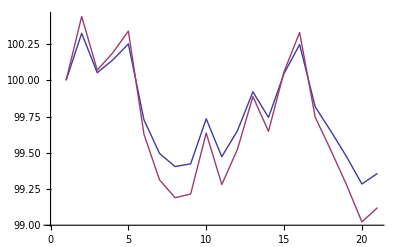

Kundenposition

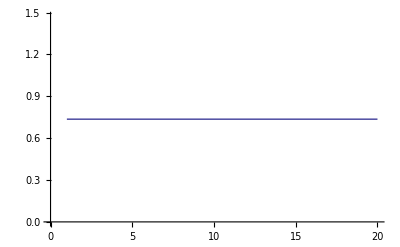

```mathematica
P0=100;M=100;S0=100;
σ=0.3;(*Volaitlität*)
r=0.04;(*risk-free Zinssatz*)
T=1/365;(*Laufzeit in jahren*)
α=0.1;(*Stock drift*)
K=20;(*Hedges täglich*)
nt=Ceiling[365 T ]K;dt=N[T/nt]
n=1;(*MonteCarlo Durchläufe*)

(*zufälliger Kunde*)qk=RandomReal[{-1,1},{nt/K}];

dW=RandomReal[NormalDistribution[],{nt n}]Sqrt[dt];
Timing[
PE=0;PV=0;

(*MonteCarlo Loop*)
For[j=0,j<n,j++,

P=Log[P0];W=0;S=S0;s={S0};p={P0};X=Preis[P0,M,σ,T];

(*Time loop*)
For[i=1,i<nt+1,i++,

W+=dW[[i]];(*Brownian Motion*)
dS=Exp[(α-σ^2/2) i dt+σ W]S0-S;(*Stock price Increment*)
q=qk[[Ceiling[i/K]]];
X+=dt r X+q S (dt (-r+α)+dW[[i]] σ) Delta[P,M,σ,T-dt*i];(*new Hedgingportfolio*)
P+=dW[[i]] q σ+dt(r+q (-r+ α-q σ^2/2));(*new Portfolio*)
S+=dS;(*new Stockprice*)

AppendTo[s,S];
AppendTo[p,Exp[P]];
]
(*PE+=Max[Exp[P]*P0-M,0];PV+=Max[Exp[P]*P0-M,0]^2;{"Mean:", Exp[-r T]PE/n,"2 StD of Mean:",2 Sqrt[Exp[-2r T]/n/(n-1)(PV-PE^2/n)]}*)
];]
Print["Aktie(rot), Kunde (blau)"];ListLinePlot[{p,s},InterpolationOrder->1]
Print["Kundenposition"]
ListLinePlot[Table[qk[[Ceiling[i/K]]],{i,1,nt}],InterpolationOrder->0]
Print["Auszahlung (const), Hedgingportfolio"];ListLinePlot[{{0,Max[p[[nt]]-M,0]},{nt,Max[p[[nt]]-M,0]}},InterpolationOrder->1]
```